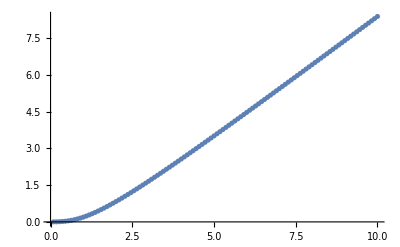

```mathematica
(*We attempt to scale our new space here to accomodate for the new densely packed situation around the origin*)
num=110;
A=1.1;
β=.9;
hbar=1;
range=10;(*Distance in fm*)
δx=range/num//N;
δk=(2π)/(num δx)//N;
spaceuni=Table[(j)*δx+.0000000001,{j,1,num}];
spacenon=Table[(spaceuni[[j]]-A ArcTan[β spaceuni[[j]]]),{j,1,num}];
kspace=Table[(j-(num/2))*δk,{j,1,num}];
absk=Table[kspace[[j]]+k0,{j,1,num}];
(*Now we look to plot the difference in the two spaces here to see if we have actually made a good choice that makes it more dense around zero.  Mainly used as a method to fix the A and β parameters here.*)
ListPlot[Table[{spaceuni[[j]],spacenon[[j]]},{j,1,num}]]
```

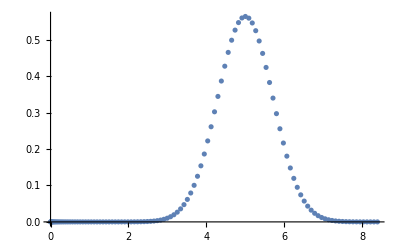

```mathematica
(*Defining the wavefunction that we are using*)
μ=1;
a0=.4;
a=1;
V0=50;(*MeV*)
x0=5;
σ0=1;
k0=10;
n=(1/π)^(1/4);(*Only the case for the above conditions*)
x=.;
ψ[x_]:=n Exp[-((x-x0)^2)/(2σ0^2)]*Exp[-I k0 (x)];
ψ0=Table[ψ[spacenon[[j]]],{j,1,num}];
ListPlot[Table[{spacenon[[j]],ψ0[[j]]*Conjugate[ψ0[[j]]]},{j,1,num}],PlotRange->All]
```

```mathematica
x=.;
t=.;
dt=.001;
delta= .1;
J=Length[spaceuni]-1;
dx=spacenon[[2]]-spacenon[[1]];
Hmax=0+1/dx^2;
τ=Hmax dt;
ii=2;
Jnτ=Table[2*(-I )^(j)BesselJ[j,τ],{j,0,20}];
Npoly=Length[Jnτ];
```

```mathematica
(*Suppose here we used the mapping onto the new space, as being the mapping that works well for the Coulomb problem, since this problem has similar short range and long range behavior as ours.*)

(*So we look to redefine only our kinetic energy, since the potential energy is still justifiably fixed that is fine, but now we must use our new form for the kinetic energy, still with our fixed space spaceuni as well as a Jacobian to show the shift.  We also define the transformation function here since we must take analytical derivatives of this to put into our function.*)
kinetic=DiagonalMatrix[Table[0,{j,1,num}]];
x[X_]:=X-A ArcTan[β X]
j=D[x[X],X];
jinverse=Table[Sqrt[spacenon[[j]]]/Sqrt[1-spacenon[[j]]],{j,1,num}];

kinetic=-(1/(2 dx^2))*(DiagonalMatrix[Table[-jinverse[[j]]2,{j,1,num}]]+DiagonalMatrix[Table[jinverse[[j]],{j,1,num-1}],1]+DiagonalMatrix[Table[jinverse[[j]]1,{j,1,num-1}],-1]);
```

```mathematica
(*Defining the Kinetic and potential energies respectively*)
Hmax=0+(1/(dx^2));
(*We need to make it so that we have a piecewise version of this matrix for the different values of space, so for the situation were 0<=x<=a*)
V[x_]:=-V0/(1+Exp[(x-a)/a0])
potential=DiagonalMatrix[Table[0,{j,1,num}]];
For[j=1,j<=num,j++,
potential[[j,j]]=V[spacenon[[j]]];
];
H=(kinetic+potential)/Hmax;
```

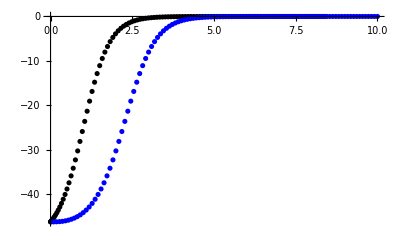

```mathematica
ListPlot[{Table[{spacenon[[j]],potential[[j,j]]},{j,1,num}],Table[{spaceuni[[j]],potential[[j,j]]},{j,1,num}]},PlotStyle->{Black, Blue},PlotRange->All]
```

```mathematica
ψt=Table[Table[0,{j,1,num}],{n,1,J+1}];
ψshebyexp=Table[Table[0,{j,1,Npoly}],{n,1,J+1}];
ψt[[;;,1]]=ψ0;
ψshebyexp[[;;,1]]=ψ0;
(*Notably we have J+1 rows and NPoly columns here*)
```

```mathematica
m=num;
For[n=1,n<m,n++,
ψshebyexp[[;;,1]]=ψt[[;;,n]];
ψshebyexp[[;;,2]]=H.(ψshebyexp[[;;,1]]);
For[jj=3, jj<Npoly,jj++,
ψshebyexp[[;;,jj]]=2 H.ψshebyexp[[;;,jj-1]];
ψshebyexp[[;;,jj]]=ψshebyexp[[;;,jj]]-ψshebyexp[[;;,jj-2]]];
ψt[[;;,n+1]]=ψshebyexp.Jnτ]
```

```mathematica
(*Now we normalize all of our results of ψt*)
For[ib=1,ib<num,ib++,
norm=.;
norm=1/(Sqrt[Sum[ψt[[j,ib]]Conjugate[ψt[[j,ib]]],{j,1,num}]]);
 ψt[[;;,ib]]=ψt[[;;,ib]] norm;]
```

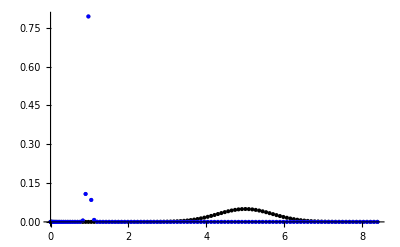

```mathematica
j=.;
ListPlot[{Table[{spacenon[[j]],ψt[[j,1]]Conjugate[ψt[[j,1]]]},{j,1,num}],Table[{spacenon[[j]],ψt[[j,5]]Conjugate[ψt[[j,5]]]},{j,1,num}],Table[{spacenon[[j]],ψt[[j,9]]Conjugate[ψt[[j,9]]]},{j,1,num}]},PlotRange->All,Joined->False,PlotStyle->{Black,Gray,Blue}]
```

```mathematica
(*Now we look to animate this function to see the propogation of these functions*)Animate[ListPlot[{Table[{spacenon[[j]],ψt[[j,b]] Conjugate[ψt[[j,b]]]},{j,1,num}],Table[{spacenon[[j]],potential[[j,j]]},{j,1,num}]},PlotRange->{{0,10},{-.25,.1}},Joined->True],{b,1,num,1}]
```

```mathematica
(*These are just the Chebyshev polynomials, so now we need to incorporate the time dependence.*)
Ψ[t_]:=ψt*Exp[-I Hmax t/(2hbar)];
Ψ[t=1][[30,1]]Conjugate[Ψ[t=1][[30,1]]];
Ψ[t=100][[30,1]]Conjugate[Ψ[t=100][[30,1]]];
```

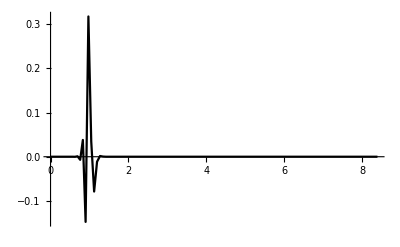

```mathematica
t=1;
ListPlot[{Table[{spacenon[[j]],Re[Ψ[t=3][[j,50]] ]},{j,1,num}]  },PlotRange->All,PlotLegends->Automatic,PlotStyle->{Black,Red,Yellow,Blue,Orange},Joined->True]
```

```mathematica
(*Now we check for the conservation of mean energy.*)
Conjugate[ψt[[;;,1]]].H. ψt[[;;,1]]
Conjugate[ψt[[;;,2]]].H. ψt[[;;,2]]
Conjugate[ψt[[;;,3]]].H. ψt[[;;,3]]
Conjugate[ψt[[;;,4]]].H. ψt[[;;,4]]
```

-5.76828×10^-8-0.40996 ⅈ

7.0844-0.359259 ⅈ

7.30096-0.407059 ⅈ

7.3062-0.392236 ⅈ

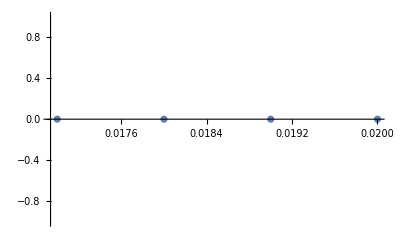

```mathematica
(*This is essentially constant here so we have conserved mean energy in time as well!*)
ListPlot[Table[{dt*j,Conjugate[ψt[[;;,j]]].H. ψt[[;;,j]]},{j,1,num}],PlotRange->All]
```

```mathematica
(*Now we check for the conservation of norm here*)
Sum[Conjugate[ψt[[j,10]]] ψt[[j,10]],{j,1,num}]
Sum[Conjugate[ψt[[j,20]]] ψt[[j,20]],{j,1,num}]
Sum[Conjugate[ψt[[j,30]]] ψt[[j,30]],{j,1,num}]
Sum[Conjugate[ψt[[j,40]]]ψt[[j,40]],{j,1,num}]
```

1.+0. ⅈ

0.+0. ⅈ

1.+0. ⅈ

1.+0. ⅈ